```mathematica
(*Sistema (14) e Jacobiano*)
aDot[a_,b_]:=Ω1-2 Sin[a]-Sin[a+b]+Sin[b];
bDot[a_,b_]:=-Ω3+Sin[a]-Sin[a+b]-2 Sin[b];
jacobian=D[{aDot[a,b],bDot[a,b]},{{a,b}}];
jacFunc=Function[{a,b},Evaluate[jacobian]];

(*Pontos fixos*)
Ω1[a_,b_]:=2 Sin[a]+Sin[a+b]-Sin[b];
Ω3[a_,b_]:=Sin[a]-Sin[a+b]-2Sin[b];

(*Elipse empirica*)
cond[a_,b_]:=Ω1[a,b]^2+Ω3[a,b]^2-Ω1[a,b]Ω3[a,b];

(*r empirico*)
r[a_,b_]:=Sqrt[3+2*(Cos[a]+Cos[a+b]+Cos[b])]/3;

(*r empirico com q's*)
q1=0.8;
q2=0.6;
q3=0.5;
rq[a_,b_]:=Sqrt[q1^2+q2^2+q3^2+2*(q1*q2*Cos[a]+q1*q3*Cos[a+b]+q2*q3*Cos[b])]/3;

(*Jacobiano*)
j11[a_,b_]:=-2 Cos[a]-Cos[a+b];
j12[a_,b_]:=-Cos[a+b]+Cos[b];
j21[a_,b_]:=Cos[a]-Cos[a+b];
j22[a_,b_]:=-Cos[a+b]-2Cos[b];
J[a_,b_]:={{j11[a,b],j12[a,b]},{j21[a,b],j22[a,b]}};

(*Maior parte real dentre os autovalores*)
Lambda[a_,b_]:=Max[Re[Eigenvalues[J[a,b]]]];
```

```mathematica
Lista de todos os pontos fixos
```

```mathematica
(*Stepsize do grid phi12xphi23*)
step=2*Pi/75;

Autovalores=Flatten[Table[{a,b,Lambda[a,b]},{a,-Pi,Pi,step},{b,-Pi,Pi,step}],1];
```

```mathematica
Lista dos pontos fixos estáveis apenas, com e sem valores de lambda
```

```mathematica
AutovaloresEstaveis=Select[Autovalores,#[[3]]<=0&];
phisEstaveis=AutovaloresEstaveis[[All,{1,2}]];
```

```mathematica
Plot dos pontos fixos phi12 e phi23 que satisfazem as condições cond = 7 (amarelo), cond = 8 (roxo), cond = 8.8 (verde), cond = 9 (preto) e cond = 9.2 (azul). Ao pontos
internos a curva vermelha são os pontos estáveis e as externas os pontos instáveis. A curva vermelha é a de Max(Re(Autovalor))=0.
```

```mathematica
contour7=ContourPlot[cond[a,b]==7,{a,-Pi,Pi},{b,-Pi,Pi},Contours->{0},ContourShading->None,PlotPoints->800,MaxRecursion->8,WorkingPrecision->30,ColorFunction->(RGBColor[212/255,175/255,55/255]&)];
contour8=ContourPlot[cond[a,b]==8,{a,-Pi,Pi},{b,-Pi,Pi},Contours->{0},ContourShading->None,PlotPoints->800,MaxRecursion->8,WorkingPrecision->30,ColorFunction->(Purple&)];
contour88=ContourPlot[cond[a,b]==8.8,{a,-Pi,Pi},{b,-Pi,Pi},Contours->{0},ContourShading->None,PlotPoints->800,MaxRecursion->8,WorkingPrecision->30,ColorFunction->(RGBColor[0,0.8,0]&)];
contour9=ContourPlot[cond[a,b]==9,{a,-Pi,Pi},{b,-Pi,Pi},Contours->{0},ContourShading->None,PlotPoints->800,MaxRecursion->8,WorkingPrecision->30,ColorFunction->(Black&)];
contour92=ContourPlot[cond[a,b]==9.2,{a,-Pi,Pi},{b,-Pi,Pi},Contours->{0},ContourShading->None,PlotPoints->800,MaxRecursion->8,WorkingPrecision->30,ColorFunction->(RGBColor[0,0,0.8]&)];
```

ContourPlot::precw: The precision of the argument function (cond[a,b]-8.8) is less than WorkingPrecision (30.).

ContourPlot::precw: The precision of the argument function (cond[a,b]-9.2) is less than WorkingPrecision (30.).

```mathematica
PhaseTransition=ListContourPlot[Autovalores,
Contours->{0},
ContourStyle->{Red},
ContourShading->None] ;
```

```mathematica
Fig=Show[
PhaseTransition,
contour7,
contour8,
contour88,
contour9,
contour92,
FrameLabel->{Style["ϕ_12",22,Black],Style["ϕ_23",22,Black]},
FrameTicksStyle->Directive[Black,16],
PlotRangePadding->0,
Epilog->{Inset[Legended[Graphics[{White}],SwatchLegend[{RGBColor[212/255,175/255,55/255],Purple,RGBColor[0,0.8,0],Black,RGBColor[0,0,0.8]},{Style["α = 7",16],Style["α = 8",16],Style["α = 8.8",16],Style["α = 9",16],Style["α = 9.2",16]},LegendMarkers->"Line",LegendLayout->"Column"]],Scaled[{0.55,0.82}] ]}
]
```

-Graphics-

```mathematica
Export["contour_ellipse_phi12phi23.png",Fig];
```

```mathematica
Apenas r estável nos pontos fixos de cond = constante através dos autovalores do Jacobiano do sistema {phi12', phi23'}.
```

```mathematica
(*Pega todos os pontos do plot e organiza em uma lista {{phi12,phi23},...}*)
```

```mathematica
abList7=Cases[Normal@contour7,Line[pts_]:>pts,∞]//Flatten[#,1]&;
abList8=Cases[Normal@contour8,Line[pts_]:>pts,∞]//Flatten[#,1]&;
abList88=Cases[Normal@contour88,Line[pts_]:>pts,∞]//Flatten[#,1]&;
abList9=Cases[Normal@contour9,Line[pts_]:>pts,∞]//Flatten[#,1]&;
abList92=Cases[Normal@contour92,Line[pts_]:>pts,∞]//Flatten[#,1]&;
```

```mathematica
(*Devolve uma lista {{phi12,phi23,r,True},...} de todos os pontos estáveis*)
```

```mathematica
stabilityData7=abList7/.{aVal_,bVal_}:>Module[{jac,eigs,stableQ},
jac=jacFunc[aVal,bVal];eigs=Eigenvalues[jac];stableQ=Max[Re[eigs]]<0;{aVal,bVal,r[aVal,bVal],stableQ}];
stablePoints7=Select[stabilityData7,#[[4]]===True&];
stabilityData8=abList8/.{aVal_,bVal_}:>Module[{jac,eigs,stableQ},
jac=jacFunc[aVal,bVal];eigs=Eigenvalues[jac];stableQ=Max[Re[eigs]]<0;{aVal,bVal,r[aVal,bVal],stableQ}];
stablePoints8=Select[stabilityData8,#[[4]]===True&];
stabilityData88=abList88/.{aVal_,bVal_}:>Module[{jac,eigs,stableQ},
jac=jacFunc[aVal,bVal];eigs=Eigenvalues[jac];stableQ=Max[Re[eigs]]<0;{aVal,bVal,r[aVal,bVal],stableQ}];
stablePoints88=Select[stabilityData88,#[[4]]===True&];
stabilityData9=abList9/.{aVal_,bVal_}:>Module[{jac,eigs,stableQ},
jac=jacFunc[aVal,bVal];eigs=Eigenvalues[jac];stableQ=Max[Re[eigs]]<0;{aVal,bVal,r[aVal,bVal],stableQ}];
stablePoints9=Select[stabilityData9,#[[4]]===True&];
stabilityData92=abList92/.{aVal_,bVal_}:>Module[{jac,eigs,stableQ},
jac=jacFunc[aVal,bVal];eigs=Eigenvalues[jac];stableQ=Max[Re[eigs]]<0;{aVal,bVal,r[aVal,bVal],stableQ}];
stablePoints92=Select[stabilityData92,#[[4]]===True&];
```

```mathematica
(*Exclui a ultima coluna que contem apenas True's*)
```

```mathematica
stablePoints7=Most/@stablePoints7;
stablePoints8=Most/@stablePoints8;
stablePoints88=Most/@stablePoints88;
stablePoints9=Most/@stablePoints9;
stablePoints92=Most/@stablePoints92;
```

```mathematica
(*Rotaciona a lista para que todos começem da mesma coordenada (phi12,phi23)=(-phi12,phi12)*)
```

```mathematica
shiftList[list_]:=Module[{pos},pos=FirstPosition[list,{x_,y_,_}/;Abs[x+y]<0.0001&&x<0&&y>0,Missing["NotFound"]];
If[pos===Missing["NotFound"],list,RotateLeft[list,First[pos]-1]]];
stablePoints7=shiftList[stablePoints7];
stablePoints8=shiftList[stablePoints8];
stablePoints88=shiftList[stablePoints88];
stablePoints9=shiftList[stablePoints9];
stablePoints92=shiftList[stablePoints92];
```

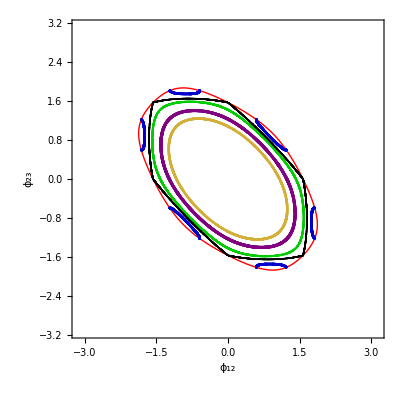

```mathematica
Show[
PhaseTransition,
ListPlot[stablePoints7[[All,{1,2}]],PlotStyle->{RGBColor[212/255,175/255,55/255]}],
ListPlot[stablePoints8[[All,{1,2}]],PlotStyle->{Purple}],
ListPlot[stablePoints88[[All,{1,2}]],PlotStyle->{RGBColor[0,0.8,0]}],
ListPlot[stablePoints9[[All,{1,2}]],PlotStyle->{Black}],
ListPlot[stablePoints92[[All,{1,2}]],PlotStyle->{RGBColor[0,0,0.8]}],
PlotRange->{{-Pi,Pi},{-Pi,Pi}},
Frame->True,
Axes->False,
FrameLabel->{Style["ϕ_12",22,Black],Style["ϕ_23",22,Black]},
FrameTicksStyle->Directive[Black,16],
PlotRangePadding->0,
AspectRatio->1
]
```

```mathematica
Abaixo é o mesmo plot mas agora com cada curva sendo pintada conforme o valor de r. A cor de cada curva está normalizada de 0 a 1, portanto a informação da diferença do
tamanho das oscilações como vista na próxima figura não aparece, entretanto percebemos que o "periodo" das oscilações é o mesmo para as diferentes "elipses"
```

```mathematica
colorFunc=ColorData["Rainbow"];
```

```mathematica
(*Faz uma lista rVals={r,...}*)
```

```mathematica
rVals7=stablePoints7[[All,3]];
rMin7=Min[rVals7];
rMax7=Max[rVals7];
coloredPoints7=Map[Function[{pt},{colorFunc[(pt[[3]]-rMin7)/(rMax7-rMin7)],Point[{pt[[1]],pt[[2]]}]}],stablePoints7];
rVals8=stablePoints8[[All,3]];
rMin8=Min[rVals8];
rMax8=Max[rVals8];
coloredPoints8=Map[Function[{pt},{colorFunc[(pt[[3]]-rMin8)/(rMax8-rMin8)],Point[{pt[[1]],pt[[2]]}]}],stablePoints8];
rVals88=stablePoints88[[All,3]];
rMin88=Min[rVals88];
rMax88=Max[rVals88];
coloredPoints88=Map[Function[{pt},{colorFunc[(pt[[3]]-rMin88)/(rMax88-rMin88)],Point[{pt[[1]],pt[[2]]}]}],stablePoints88];
rVals9=stablePoints9[[All,3]];
rMin9=Min[rVals9];
rMax9=Max[rVals9];
coloredPoints9=Map[Function[{pt},{colorFunc[(pt[[3]]-rMin9)/(rMax9-rMin9)],Point[{pt[[1]],pt[[2]]}]}],stablePoints9];
rVals92=stablePoints92[[All,3]];
rMin92=Min[rVals92];
rMax92=Max[rVals92];
coloredPoints92=Map[Function[{pt},{colorFunc[(pt[[3]]-rMin92)/(rMax92-rMin92)],Point[{pt[[1]],pt[[2]]}]}],stablePoints92];
```

```mathematica
Show[
Graphics[coloredPoints7],
Graphics[coloredPoints8],
Graphics[coloredPoints88],
Graphics[coloredPoints9],
Graphics[coloredPoints92],
PlotRange->{{-Pi,Pi},{-Pi,Pi}},
Frame->True,
Axes->False,
FrameLabel->{Style["ϕ_12",22,Black],Style["ϕ_23",22,Black]},
FrameTicksStyle->Directive[Black,16],
PlotRangePadding->0,
AspectRatio->1]
```

-Graphics-

```mathematica
Valores de r calculados de acordo com a expressão (15) para esses pontos fixos estáveis são mostrados na figura abaixo em curvas continuas.
As curvas tracejadas representam os valores de r de acordo com a expressao (18).
```

```mathematica
(*Pega cada uma das listas rVals e reescala o numero de pontos para ficar de 0 a 1*)
```

```mathematica
rescaleXs[data_]:=Rescale[Range[Length[data]],{1,Length[data]},{0,1}]
rVals7scaled=Transpose[{rescaleXs[rVals7],rVals7}];
rVals8scaled=Transpose[{rescaleXs[rVals8],rVals8}];
rVals88scaled=Transpose[{rescaleXs[rVals88],rVals88}];
rVals9scaled=Transpose[{rescaleXs[rVals9],rVals9}];
rVals92scaled=Transpose[{rescaleXs[rVals92],rVals92}];
```

```mathematica
Fig=Show[
ListLinePlot[rVals7scaled,PlotStyle->{RGBColor[212/255,175/255,55/255]}],
ListLinePlot[rVals8scaled,PlotStyle->{Purple}],
ListLinePlot[rVals88scaled,PlotStyle->{RGBColor[0,0.8,0]}],
ListLinePlot[rVals9scaled,PlotStyle->{Black}],
(*ListLinePlot[rVals92scaled,PlotStyle->{RGBColor[0,0,0.8]}],*)
Plot[Sqrt[5+4*Sqrt[1-7/9]]/3,{x,0,1},PlotStyle->{RGBColor[212/255,175/255,55/255],Dashed}],
Plot[Sqrt[5+4*Sqrt[1-8/9]]/3,{x,0,1},PlotStyle->{Purple,Dashed}],
Plot[Sqrt[5+4*Sqrt[1-8.8/9]]/3,{x,0,1},PlotStyle->{RGBColor[0,0.8,0],Dashed}],
Plot[Sqrt[5+4*Sqrt[1-9/9]]/3,{x,0,1},PlotStyle->{Black,Dashed}],
(*Plot[Sqrt[5+4*Sqrt[1-9.2/9]]/3,{x,0,1},PlotStyle->{RGBColor[0,0,0.8],Dashed}],*)
PlotRange->{{0,1},{0.74,0.88}},
Frame->True,
Axes->False,
FrameLabel->{Style["Nada",22,White],Style["r",22,Black]},
FrameTicksStyle->{{Directive[Black,FontSize->16],Directive[Black,FontSize->16]},(*left & right y-axis*)
{Directive[White,FontSize->16],Directive[White,FontSize->16]}(*bottom & top x-axis*)},
PlotRangePadding->0,
AspectRatio->1]
```

-Graphics-

```mathematica
Export["r_ellipses_phi12phi23.png",Fig];
```

```mathematica
LegendAlpha=LineLegend[{RGBColor[212/255,175/255,55/255],Purple,RGBColor[0,0.8,0],Black,RGBColor[0,0,0.8]},{Style["α = 7",16],Style["α = 8",16],Style["α = 8.8",16],Style["α = 9",16]},LegendLayout->"Column"]
Export["LegendAlpha.png",LegendAlpha];
```

```mathematica
LegendOmega=LineLegend[{RGBColor[238/255,0,0],RGBColor[26/255,174/255,92/255],RGBColor[0,0,205/255]},{Style["ω = 1.5",16],Style["ω = 2.5",16],Style["ω = 3.5",16]},LegendLayout->"Column"]
Export["LegendOmega.png",LegendOmega];
```

```mathematica
Caso não forcemos a equação da elipse, mas ao invés forcemos que r seja constante, chegamos que as curvas de nivel serão quase elipses como podemos ver na figura abaixo.
As curvas tracejadas são as elipses equanto que as curvas continuas representam as curvas de nivel de r constante.
```

```mathematica
Fig=Import["/home/leonardo/Documents/R/Artigo/3osc/r_const_w1w3.png"]
```

-Graphics-

```mathematica
Export["r_cte_w1w3.png",Fig];
```

```mathematica
Esse é um simples Heatmap de r calculado pela expressão analítica (15). Vemos que ele é definido em toda a região do espaço e que as "elipses" vão deixando de ser elipses
conforme aumentamos cond = constante. Em seguida mostramos a maior parte real dos autovalores do Jacobiano do sistema {phi12', phi23'} calculado nesses pontos, quando o
maior autovalor é zero então ambos tem parte real negativa e portanto o ponto é estável. Em terceiro temos o plot reparametrizado para o plano dos Omegas, é o plot apenas
dos pontos estáveis com o mesmo valor de r do primeiro plot e valores de omega definidos pela equação de \dot{phi}=0. Juntando todos os plots de pontos estáveis, percebemos
que a região de r estável é a mesma descrita pelo segundo heatmap, que é uma elipse meio retangular.
Por último plotamos novamente os pontos estáveis no plano dos omegas, mas agora para a equação de r com os q's. Vemos
```

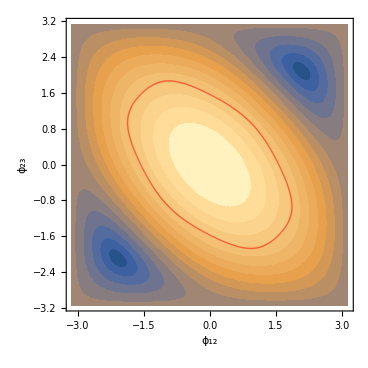

```mathematica
Fig=Show[
ContourPlot[r[a,b],{a,-Pi,Pi},{b,-Pi,Pi},
Contours->15,
ContourLines->False],
PhaseTransition,
FrameLabel->{Style["ϕ_12",22,Black],Style["ϕ_23",22,Black]},
FrameTicksStyle->Directive[Black,16],
PlotRangePadding->0]
```

```mathematica
Export["r_analitico_phi12phi23.png",Fig];
```

```mathematica
maxValue=FindMaximum[r[a,b],{a,-Pi,Pi},{b,-Pi,Pi}]//First;
minValue=FindMinimum[r[a,b],{a,-Pi,Pi},{b,-Pi,Pi}]//First;
```

```mathematica
Fig=BarLegend[{"M10DefaultDensityGradient",{minValue,maxValue}},LabelStyle->{Black,FontSize->12}]
```

```mathematica
Export["colorbar_phi12phi23.png",Fig];
```

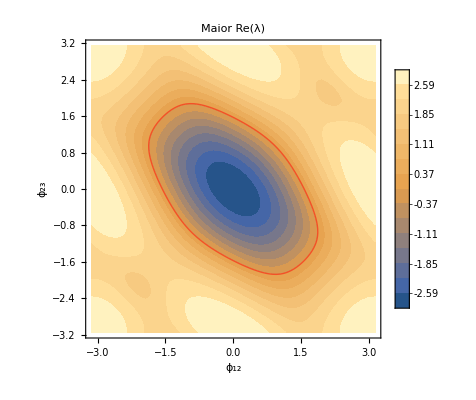

```mathematica
Show[ListContourPlot[Autovalores,
InterpolationOrder->1,
Contours->15,
ContourLines->False,
PlotLegends->Automatic,
ColorFunction->"M10DefaultDensityGradient"],
PhaseTransition,
PlotLabel->"Maior Re(λ)",
FrameLabel->{Style["ϕ_12",22,Black],Style["ϕ_23",22,Black]},
FrameTicksStyle->Directive[Black,16],
PlotRangePadding->0]
```

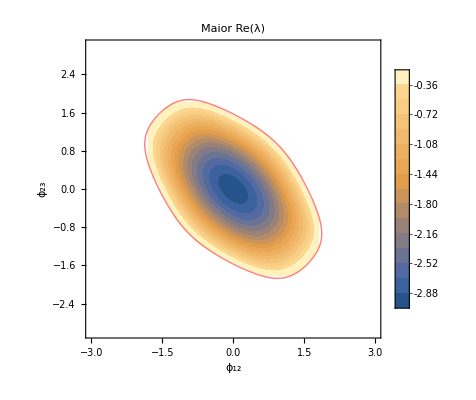

```mathematica
Show[ListContourPlot[AutovaloresEstaveis,
InterpolationOrder->1,
Contours->15,
ContourLines->False,
PlotLegends->Automatic,
ColorFunction->"M10DefaultDensityGradient"],
PhaseTransition,
PlotLabel->"Maior Re(λ)",
FrameLabel->{Style["ϕ_12",22,Black],Style["ϕ_23",22,Black]},
FrameTicksStyle->Directive[Black,16],
PlotRange->{{-3,3},{-3,3}},
PlotRangePadding->0]
```

```mathematica
Calculo do menor valor de r na curva vermelha, curva onde r atinge menor valor
```

```mathematica
rEstaveis=r@@@phisEstaveis;
omega1Estavel=Ω1@@@phisEstaveis;
omega3Estavel=Ω3@@@phisEstaveis;
omegaEstaveis=Transpose[{omega1Estavel,omega3Estavel}];
phisrEstaveis=MapThread[Append,{omegaEstaveis,rEstaveis}];
```

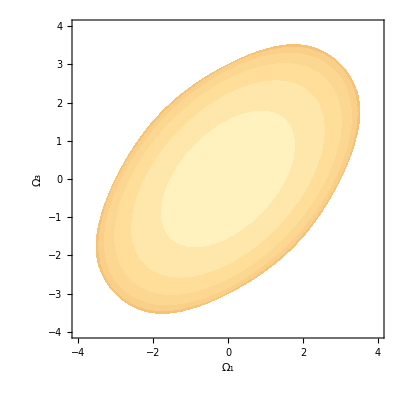

```mathematica
Fig=Show[ListContourPlot[phisrEstaveis,
Contours->5,
ContourLines->False,
ContourShading->True,
ColorFunction->"M10DefaultDensityGradient",
InterpolationOrder->2,
Mesh->None,
ColorFunctionScaling->False,
PlotRange->{{-4,4},{-4,4}},
FrameLabel->{Style["Ω₁",22,Black],Style["Ω₃",22,Black]},
FrameTicksStyle->Directive[Black,16],
PlotRangePadding->0]]
```

```mathematica
Export["r_analitico_w1w3.png",Fig];
```

```mathematica
rqEstaveis=rq@@@phisEstaveis;
omega1Estavel=Ω1@@@phisEstaveis;
omega3Estavel=Ω3@@@phisEstaveis;
omegaEstaveis=Transpose[{omega1Estavel,omega3Estavel}];
phisrqEstaveis=MapThread[Append,{omegaEstaveis,rqEstaveis}];
```

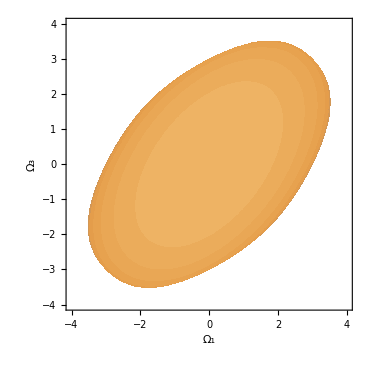

```mathematica
Fig=Show[ListContourPlot[phisrqEstaveis,
Contours->5,
ContourLines->False,
ContourShading->True,
ColorFunction->"M10DefaultDensityGradient",
InterpolationOrder->2,
Mesh->None,
ColorFunctionScaling->False,
PlotRange->{{-4,4},{-4,4}},
FrameLabel->{Style["Ω₁",22,Black],Style["Ω₃",22,Black]},
FrameTicksStyle->Directive[Black,16],
PlotRangePadding->0]]
```

```mathematica
Export["rq_analitico_w1w3.png",Fig];
```